Region[a^2+r^2-2 a r Cos[t]<1/25]

```mathematica
Region[(+x)^2+y^2<1/25]
```

Region[x^2+y^2<1/25]

```mathematica
Integrate[1,{x,y}∈Region[Disk[{r,0},1/25]]]
```

ConditionalExpression[π/625,r∈ℝ]

```mathematica
Integrate[2(Sqrt[5-1/Sqrt[a^2+r^2-2a*r*Cos[θ]]]/(2Pi*a))^3*BesselJ[1,2a*Sqrt[5-1/Sqrt[a^2+r^2-2a*r*Cos[θ]]]],{a,θ}∈ImplicitRegion[a^2+r^2-2a*r*Cos[θ]>1/25,{a,θ}]]
```

Integrate[(BesselJ[1,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a^3 π^3),{a ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25,{a,θ}],θ ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25,{a,θ}]}]

```mathematica
Integrate[2(Sqrt[5-1/Sqrt[a^2+r^2-2a*r*Cos[θ]]]/(2Pi*a))^3*BesselJ[1,2a*Sqrt[5-1/Sqrt[a^2+r^2-2a*r*Cos[θ]]]],{a,θ}∈ImplicitRegion[a^2+r^2-2a*r*Cos[θ]>1/25,{a,θ}]]
```

∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25,{a,θ}]) (BesselJ[1,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a^3 π^3)

```mathematica
Simplify[∫_({a,θ}∈ImplicitRegion[a^2-2 a r cos(θ)+r^2>1/25,{a,θ}]) ((5-1/(√(a^2-2 a r cos(θ)+r^2)))^(3/2) 32 a √(5-1/(√(a^2-2 r cos(θ) a+r^2))))/(4 π^3 a^3)]
```

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25,{a,θ}]) (BesselJ[3,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a^3 π^3),{r,0,1}]
```

-Graphics-

```mathematica
∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25,{{a,0,Infinity},{θ,0,Pi}}]) (BesselJ[1,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a π^3)
```

∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[1,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a π^3)

```mathematica
Simplify[%1]
```

∫_({a,θ}∈ImplicitRegion[a^2-2 a r cos(θ)+r^2>1/25∧a≥0∧0≤θ≤π,{a,θ}]) ((5-1/(√(a^2-2 a r cos(θ)+r^2)))^(3/2) 12 a √(5-1/(√(a^2-2 r cos(θ) a+r^2))))/(4 π^3 a)

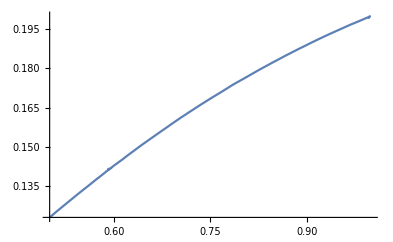

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[1,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a π^3),{r,0.5,1}]
```

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[1,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a π^3),{r,0,4}]
```

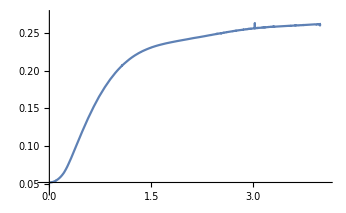

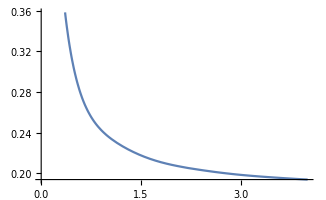

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[a≥0&&0≤θ≤π,{a,θ}]) 1/(4 a π^3)BesselJ[1,2 a √(5+1/(√(a^2+r^2-2 a r Cos[θ])))] (5+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2)*Sin[θ],{r,0,4}]
```

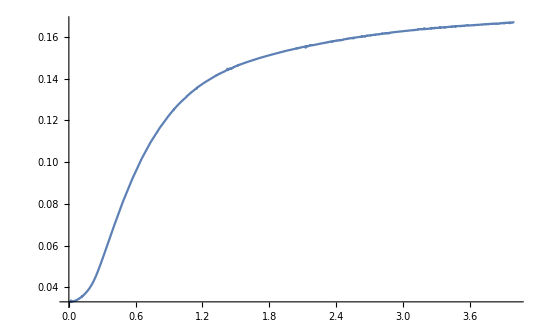

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25&&a≥0&&0≤θ≤π,{a,θ}]) 1/(4 a π^3)BesselJ[1,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2)*Sin[θ],{r,0,4}]
```

```mathematica
Show[%7,ImageSize->Medium]
```

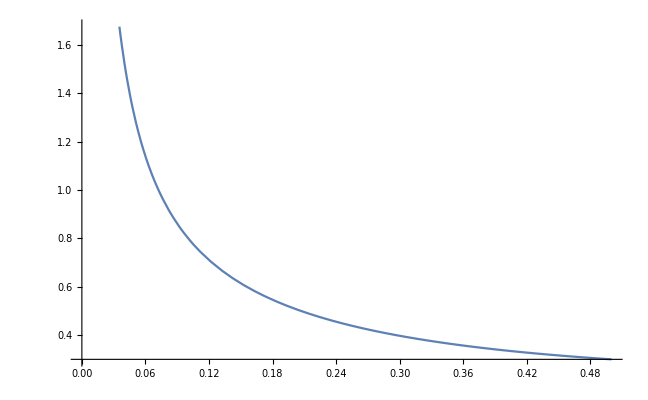

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[1,2 a √(5+1/(√(a^2+r^2-2 a r Cos[θ])))] (5+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2))/(4 a π^3)*Sin[θ],{r,0,0.5}]
```

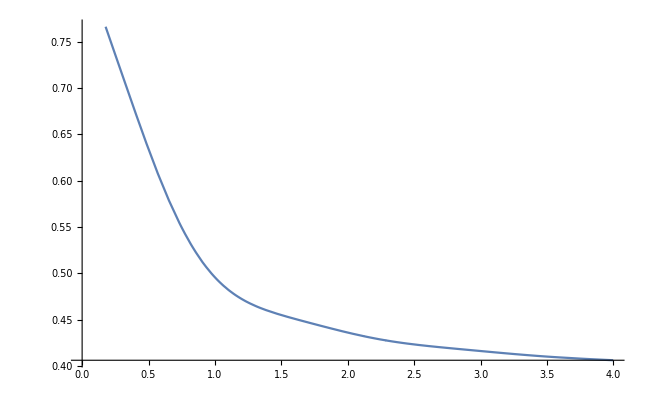

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[a≥0&&0≤θ≤π,{a,θ}]) 1/(2 a π^2)BesselJ[3,2 a √(5+1/(√(a^2+r^2-2 a r Cos[θ])))] (5+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2)*Sin[θ],{r,0,4}]
```

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[1/25>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) 1/(2 a π^2)BesselJ[3,2 a √(-5+1/(√(a^2+r^2-2 a r Cos[θ])))] (-5+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2)*Sin[θ],{r,0,4}]
```

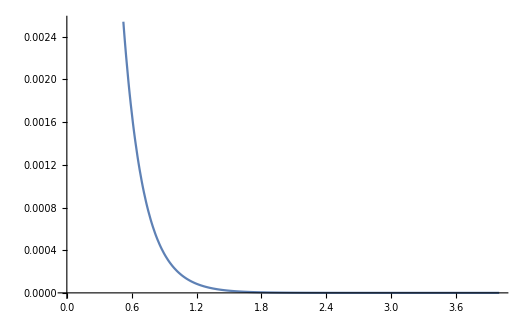

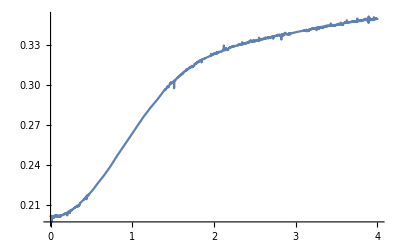

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[r^2-2 r Cos[θ] a+a^2>1/25&&a≥0&&0≤θ≤π,{a,θ}]) 1/(2 a π^2)BesselJ[3,2 a √(5-1/(√(a^2+r^2-2 a r Cos[θ])))] (5-1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2)*Sin[θ],{r,0,4}]
```

```mathematica
Show[%1,ImageSize->{1181,218},AspectRatio->Full]
```

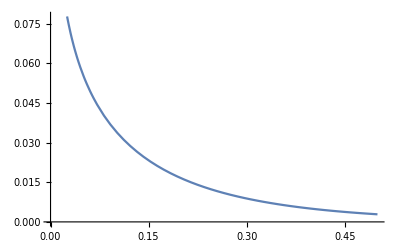

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[1/25>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) 1/(2 a π^2)BesselJ[3,2 a √(-5+1/(√(a^2+r^2-2 a r Cos[θ])))] (-5+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2)*Sin[θ],{r,10^(-6),0.5}]
```

```mathematica
NIntegrate[∫_({a,θ}∈ImplicitRegion[1/25>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-5+1/(√(a^2+r^2-2 a r Cos[θ])))] (-5+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,5}]
```

0.0118215

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[1/25>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,4}]
```

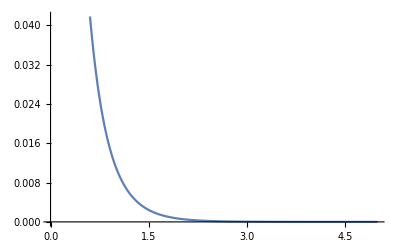

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,5}]
```

```mathematica
NIntegrate[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,Infinity},MaxRecursion->12]
```

0.145183

```mathematica
NIntegrate[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,2}]
```

0.144968

```mathematica
NIntegrate[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,Infinity},MaxRecursion->12]
```

0.145184

```mathematica
NIntegrate[∫_({a,θ}∈ImplicitRegion[4>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-1+2/(√(a^2+r^2-2 a r Cos[θ])))] (-1+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,Infinity},MaxRecursion->12]
```

0.19883

```mathematica
NIntegrate[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (2r^2*BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(a π),{r,0,Infinity},MaxRecursion->12]
```

7.99436093340834528133189189915`15.954589770191005*^737991742809999+3.337162237003145139991562035492`15.954589770191005*^737991742810000 ⅈ

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (2r^2*BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(a π),{r,0,2}]
```

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (2r^2*BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(a π),{r,2,4}]
```

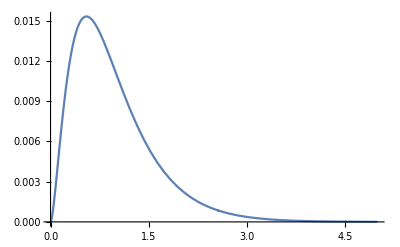

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[1>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (r^2*BesselJ[3,2 a √(-2+2/(√(a^2+r^2-2 a r Cos[θ])))] (-2+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,5}]
```

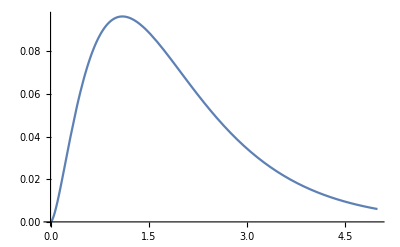

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[4>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (4Pi r^2*BesselJ[3,2 a √(-0.5+1/(√(a^2+r^2-2 a r Cos[θ])))] (-0.5+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,5}]
```

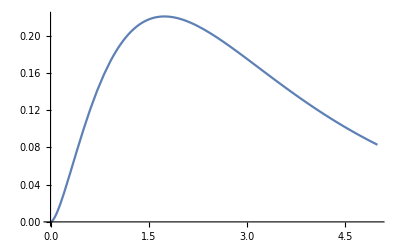

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[25>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (4Pi r^2*BesselJ[3,2 a √(-0.2+1/(√(a^2+r^2-2 a r Cos[θ])))] (-0.2+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,5}]
```

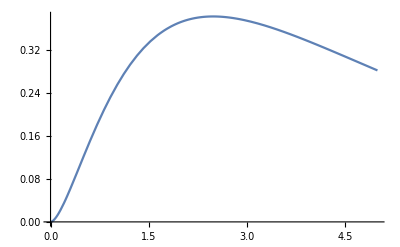

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[100>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (4Pi r^2*BesselJ[3,2 a √(-0.1+1/(√(a^2+r^2-2 a r Cos[θ])))] (-0.1+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,5}]
```

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[10000>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (4Pi r^2*BesselJ[3,2 a √(-0.01+1/(√(a^2+r^2-2 a r Cos[θ])))] (-0.01+1/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,0,40}]
```